```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/ninel/Documents/potts/potts

```mathematica
res0=Partition[<<"output.txt",3];
```

```mathematica
res={res0[[#,1]],res0[[#,2]]~Join~res0[[#,3]]}&/@Range[Length@res0];
```

```mathematica
(*desired = {2100,0.66,1.7,6.4};
dd=              {1000.0, 0.11,0.8,2.4};*)
(*desired = {1400,0.8,4.0,2.8};
dd=              {800.0, 0.09,2.1,1.6};*)
desired = {2500,0.84,1.9,1.7,5.3,2100,0.66,1.7,1.7,6.4};
dd=              {1000.0, 0.09,1.0,0.8,1.5,1000.0, 0.11,0.8, 0.6,2.4};
(*desired = {1400,0.8,4.0,3.0,2.8,1300,0.63,2.5,2.2,4.8};
dd=              {800.0, 0.09,2.1,1.4,1.6,800.0, 0.12,1.8,1.4,2.5};*)
(*desired = {1000,0.79,2.5,3.3};
dd=              {400.0, 0.11,1.4,1.3};*)
(*desired = {900,0.7,2.4,4.0};
dd=              {300.0, 0.1,1.2,1.3};*)
```

```mathematica
params={1,2,3,4,5};
```

```mathematica
w={5,1,1,0,0.5,5,1,1,0,0.5}
```

{5,1,1,0,0.5,5,1,1,0,0.5}

```mathematica
res[[-1,2]]
```

{568.918,0.859845,1.60715,1.50597,3.08456,541.032,0.773566,1.73188,1.55083,3.50474}

```mathematica
list=SortBy[{Map[#&,res[[;;,1,2;;]]],Map[#&,res[[;;,2]]],Map[Norm[(#-desired)/dd w]&,res[[;;,2]]]}ᵀ,First]
```

{{{100},{568.918,0.859845,1.60715,1.50597,3.08456,541.032,0.773566,1.73188,1.55083,3.50474},12.4939},{{200},{581.764,0.836036,1.6784,1.55202,3.09007,545.722,0.748492,1.77703,1.58417,3.44782},12.4102},{{300},{588.34,0.831075,1.72128,1.58519,3.20037,547.035,0.730071,1.8093,1.60353,3.40228},12.3693},{{400},{591.283,0.821715,1.74806,1.60062,3.19301,552.224,0.715701,1.84485,1.6321,3.51992},12.336},{{500},{594.278,0.815883,1.76784,1.6162,3.13051,549.164,0.710231,1.83283,1.63147,3.48197},12.3345},{{600},{594.517,0.813745,1.80308,1.64482,3.20404,553.745,0.701886,1.84744,1.63471,3.49715},12.3155},{{700},{596.051,0.813724,1.81642,1.66015,3.12684,556.399,0.70032,1.83379,1.63491,3.59393},12.301},{{800},{600.717,0.813212,1.84349,1.67814,3.19118,553.983,0.690942,1.84466,1.64051,3.55028},12.2876},{{900},{601.162,0.811133,1.84545,1.677,3.19118,554.948,0.686452,1.86071,1.63121,3.5351},12.2831},{{1000},{602.727,0.807821,1.86261,1.6871,3.11765,556.897,0.681587,1.86479,1.64631,3.51613},12.2728},{{1100},{602.77,0.803259,1.86231,1.68203,3.27022,557.901,0.683882,1.86715,1.64493,3.43833},12.2693},{{1200},{603.534,0.802313,1.84335,1.66931,3.23346,559.448,0.680582,1.87737,1.64723,3.5389},12.2613},{{1300},{603.165,0.806314,1.85402,1.68812,3.23713,561.327,0.67743,1.88487,1.64475,3.51803},12.2553}}

```mathematica
list[[;;,2,1]]
```

{568.918,581.764,588.34,591.283,594.278,594.517,596.051,600.717,601.162,602.727,602.77,603.534,603.165}

```mathematica
ToPlot[x_]:={list[[;;,1,1]],Map[(x[[1]]-#)/(x[[1]]-x[[-1]])&,x]}ᵀ
```

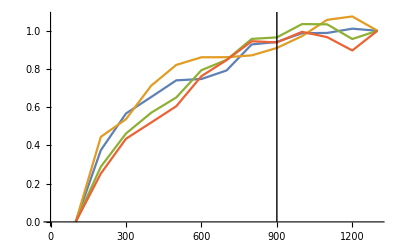

```mathematica
ListLinePlot[Map[ToPlot,list[[;;,2,{1,2,3,4}]]ᵀ],Epilog->{Line[{{900,0},{900,1.5}}]}]
```

```mathematica
{Mean[#],StandardDeviation[#]}&/@(list[[;;,2]]ᵀ)
```

{{592.957,10.2971},{0.820677,0.0161682},{1.77783,0.0827879},{1.62629,0.0599967},{3.1636,0.0574048},{551.732,5.34311},{0.711194,0.0291697},{1.82858,0.0413956},{1.62133,0.0298258},{3.49888,0.0544592}}

{{2510.43,24.3821},{0.853525,0.0135146},{1.87675,0.099866},{1.68705,0.080998},{5.80698,0.300612},{2127.66,21.4296},{0.668469,0.0211399},{1.80621,0.114719},{1.56622,0.0736075},{8.05943,0.373464}}

{{70.25,0.77,183.644,930.372,32.906,470.196,630.78,2.54},{31.266,0.05,42.7027,171.059,16.7588,78.4803,191.399,1.36795}}

{{71.204,0.886,206.768,891.452,34.562,411.6,1012.68,2.242},{28.7506,0.0604979,42.0012,221.438,13.6237,91.1817,197.709,1.45229}}

```mathematica
list=SortBy[{Map[#-res[[-1,1]]&,res[[;;,1]]],Map[(#-desired)/dd^2&,res[[;;,2,params]]],Map[Norm[(#-desired)/desired w]&,res[[;;,2,params]]]}ᵀ,Last][[;;10]]
```

{{{0,32.05,-0.31,-66.09,248.21,1.81,152.27,594.19,-1.89},{0.0000820625,3.87807,0.0402178,-0.112085},0.0742864},{{0,-0.27,-0.28,7.51,19.54,-20.66,86.36,401.39,-0.43},{-0.000194766,3.19988,-0.0745761,0.00455166},0.0824196},{{0,17.14,-0.27,-42.32,-31.04,-15.25,-12.79,458.16,-0.85},{2.38281×10^-6,-3.95631,0.126823,0.219807},0.12933},{{0,31.83,-0.34,-60.04,148.9,-10.61,7.65,292.11,-0.83},{-0.000280055,-6.67121,0.109414,0.0519648},0.141364},{{0,6.,-0.42,-88.16,102.71,-9.89,65.43,476.49,-1.95},{-0.00083532,0.329063,0.115423,-0.0542406},0.162079},{{0,6.76,-0.36,-68.67,244.68,-21.4,165.33,-102.51,-0.75},{-0.0000533594,-7.39117,-0.123164,0.2786},0.165232},{{0,32.12,-0.39,-80.68,35.28,-24.66,27.27,105.51,0.33},{-0.000629422,-8.64778,-0.00500518,0.117395},0.16913},{{0,42.01,-0.34,-81.61,147.31,4.44,259.62,186.32,-0.08},{0.000507922,0.38377,-0.188903,0.0955849},0.170797},{{0,-4.38,-0.33,-57.84,-5.78,-16.72,229.52,225.53,-1.93},{0.0000809922,1.6468,-0.219649,0.067137},0.175369},{{0,-2.09,-0.17,-76.,66.62,-14.7,-3.4,363.68,-1.79},{0.000764852,2.00324,-0.141767,0.373426},0.193426}}

```mathematica
init=Position[list[[;;,1]],{0.,0.,0.,0.,0.,0.,0.}][[1,1]];
```

```mathematica
list[[;;init]]
```

{{{0.,-1.36,0.29,36.98,-888.14,0.901,-41.59},{0.0000551875,2.43258,0.163397,0.290053},0.153297},{{0.,0.,0.,0.,0.,0.,0.},{-0.000214477,5.69811,0.30904,0.0813692},0.190317}}

```mathematica
FirstNZ[x_]:=Module[{c=Map[If[#==0.,0,1]&,x],p},p=Position[c,1];If[p=={},0,x[[p[[1,1]]]]]]
```

```mathematica
Map[FirstNZ,list[[;;init]][[;;,1]]ᵀ]
```

{0,-1.36,0.29,36.98,-888.14,0.901,-41.59}

```mathematica
Renormalize[x_]:=x[[2;;]]
```

```mathematica
ch=res[[-1,1]]+Map[FirstNZ,list[[;;init]][[;;,1]]ᵀ]
```

{1.,5.74,1.08,61.77,1831.74,30.058,243.34}

```mathematica
Renormalize[ch]
```

{5.74,1.08,61.77,1831.74,30.058,243.34}